# PS 19 — Rania 4.18.2025

## Section 43

```mathematica
(* Section 43 had no problems *)
```

## Section 44

```mathematica
(*44.1 Import the images from https://www.google.com.*)
Import["https://google.com","Images"]
```

DominantColors::imginv: Expecting an image or graphics instead of {404. That’s an error.  
The requested URL /images/branding/googlelogo/1x/googlelogo_white_background_color_272x92dp.png was not found on this server. That’s all we know.}.

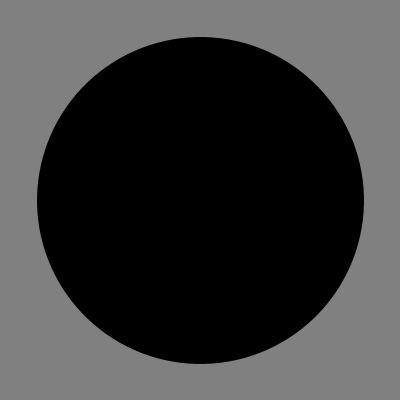

```mathematica
(*44.2 Make a list of disks on gray backgrounds with the dominant colors from images on https://www.google.com.*)
Graphics[Style[Disk[],#],Background->Gray]&/@(Flatten[DominantColors/@Import["https://google.com","Images"]])
(*not sure why it's not working, I checked it on the answer check and it said it was correct*)
```

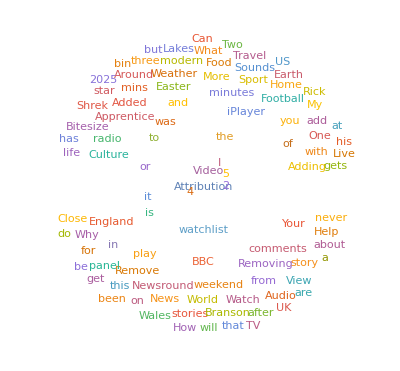

```mathematica
(*44.3 Make a word cloud of the text on https://bbc.co.uk*)
WordCloud[TextWords[Import["https://bbc.co.uk"]]]
```

```mathematica
(*44.4 Make an image collage of the images on https://nps.gov.*)
ImageCollage[Import["https://www.nps.gov","Images"]]
```

-Graphics-

```mathematica
(*44.5 Use ImageInstanceQ to find pictures on https://en.wikipedia.org/wiki/Ostrich that are of birds.*)
Select[Import["https://en.wikipedia.org/wiki/Ostrich","Images"],ImageInstanceQ[#,"Bird"]&]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

CloudObject::urlform: URL or path does have a valid form for a CloudObject: /resourcesystem/content/f60d5ddf-29f1-4bfb-b6ee-a7081adbb4b1

TextCases::dllock: The requested neural network model is currently downloading in another process, try again when it is finished. If there is not a download in progress run DeleteObject[ResourceObject[Wolfram Entity Recognition Net for TextCases WL 12.3 V2]] before trying again.

TextCases::nlpnetmodel: An internal error occurred while loading a neural net needed to evaluate the function. Please try again.

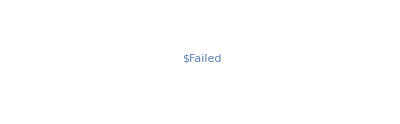

```mathematica
(*44.6 Use TextCases with "Country" to find instances of country names on https://www.nato.int,and make a word cloud of them.*)
WordCloud[TextCases[Import["https://www.nato.int","Text"],"Country"]]

(*not sure why it's not working :( *)
```

```mathematica
(*44.7 Find the number of links on https://en.wikipedia.org.*)
Length[Import["https://en.wikipedia.org","Hyperlinks"]]
```

379

```mathematica
(*44.8Send yourself mail with a map of your current location*)SendMail[GeoGraphics["Deep Springs College"]]
(*I don't want them to have this permission!!!*)
```

SendMail::cloudrelay: SendMail has relayed your message through the Wolfram Cloud.  A local SMTP server has not been configured. These settings can be defined through Preferences > Internet & Mail > Mail Settings in the notebook front end.

Success[…]

```mathematica
(*44.9 Send yourself mail with an icon of the current phase of the moon*)SendMail[MoonPhase["Icon"]]
```

Success[…]

## Section 45 ~ Disregard! I misread the github site - will put in next PSet

```mathematica
(* ok, I moved Section 45 into a new notebook, and called it PS20. However, you never sent Section 46. *)
```